```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"AnSEL.m"]
```

# AnSEL - Analysis and Simplification of Equations with Loops

## Exports

```mathematica
SetLoopMomentumName::usage=""

Route::usage=""
Route[expr_FEq]/;Head[$GlobalSetup]=!=Symbol:=Route[$GlobalSetup,expr];

FSimplify::usage=""
FSimplify[expr_FEq]/;Head[$GlobalSetup]=!=Symbol:=FSimplify[$GlobalSetup,expr];
```

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

If[ModuleLoaded[FEDeriK]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

ModuleLoaded[AnSEL]=True;

$loopMomentumName="l";
Unprotect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
ClearAll@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Protect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Unprotect[$availableLoopMomenta];
$availableLoopMomenta=Table[Symbol[$loopMomentumName<>ToString[idx]],{idx,1,50}];
Protect[$availableLoopMomenta];
```

```mathematica
SetLoopMomentumName[name_String]:=Module[{},
Unprotect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
$loopMomentumName=name;
ClearAll@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Protect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Unprotect[$availableLoopMomenta];
$availableLoopMomenta=Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Protect[$availableLoopMomenta];
];
```

```mathematica
$FunKitDirectory=SelectFirst[Join[{FileNameJoin[{$UserBaseDirectory,"Applications","FunKit"}],FileNameJoin[{$BaseDirectory,"Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Packages","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","ExtraPackages","FunKit"}]},Select[$Path,StringContainsQ[#,"FunKit"]&]],DirectoryQ[#]&]<>"/";
```

## Index routing

```mathematica
(*A convenience function to quickly obtain the index structure of a given field.*)
FieldSetupIndices[setup_,field_]:=Module[{},
List@@SelectFirst[
Flatten@Values[setup["FieldSpace"]],
Head[#]===field&
]
];
```

```mathematica
Route::undeterminedFields="Cannot route indices in expressions with undetermined fields.";
Route::momentaFailed="Cannot route momenta in the given expression.";

Route[setup_,expr_FTerm]:=Module[
{openIndices,closedIndices,objects,
ret=ReduceFTerm[setup,ReduceIndices[setup,expr]],doFields,idx,a,
indPos,assocField,subObj,subMom,subExtMom,
indStruct,externalIndices,externalMomenta,
f,momRepl,A1111111,AA111111,i,mom,loopMomenta
},

(*We first get all closed, open indices and all indexed objects.*)
doFields=replFields[setup];
openIndices=Sort@GetOpenSuperIndices[setup,ret];
closedIndices=GetClosedSuperIndices[setup,ret];
objects=ExtractObjectsWithIndex[setup,ret]//.doFields;

(*If there are any undetermined fields, we cannot route indices.*)
If[MemberQ[objects[[All,1]],AnyField,{1,4}],Message[Route::undeterminedFields];Abort[]];

(*As a first step, we insert the correct index structures into all superindices and define momentum variables at every single vertex.
We loop over all closed indices.*)
Do[
(*The indexed object we currently modify. There are always two and we simply grab the first.*)
subObj=Select[objects,MemberQ[#,closedIndices[[idx]],Infinity]&][[1]];
(*The position of the current index inside the subObj*)
indPos=FirstPosition[subObj[[2]],closedIndices[[idx]]][[1]];
(*See what kind of field is associated with the index*)
assocField=subObj[[1,indPos]];
(*Grab the index structure of this field from the setup and assign a new momentum variable*)
indStruct=Map[If[MatchQ[#,_Symbol],Unique[SymbolName[#]],#]&,FieldSetupIndices[setup,assocField],{1,3}];
indStruct[[1]]=loopMomentum[indStruct[[1]]];

(*replace all occurences of the superindex with the fitting index structure. 
We want to keep the index sign in the momenta, but remove it from the group indices*)
ret=ret/.closedIndices[[idx]]->indStruct;
ret=ret/.(-indStruct[[2]])->indStruct[[2]];
objects=objects/.closedIndices[[idx]]->indStruct;
objects=objects/.(-indStruct[[2]])->indStruct[[2]];

,{idx,1,Length[closedIndices]}];

(*Next, we treat the external superindices. We assign to each an open group structure and a new momentum p1,p2,... 
Momentum conservation is already enforced here, i.e. ∑_i Subscript[p, i]=0 and we choose Subscript[p, n]=-∑_(i<n) Subscript[p, i] for the last momentum Subscript[p, n].*)
externalIndices=Table[{},{idx,1,Length[openIndices]}];
Do[
(*see above*)
subObj=Select[objects,MemberQ[#,openIndices[[idx]],Infinity]&][[1]];
indPos=FirstPosition[subObj[[2]],openIndices[[idx]]][[1]];
assocField=subObj[[1,indPos]];
indStruct=Map[If[MatchQ[#,_Symbol],Symbol[SymbolName[#]<>ToString[idx]],#]&,FieldSetupIndices[setup,assocField],{1,3}];

(*Subscript[p, n]=-∑_(i<n) Subscript[p, i]*)
If[idx===Length[openIndices],indStruct[[1]]=-Total[Values[externalIndices][[;;idx-1,1]]]];

ret=ret/.openIndices[[idx]]->indStruct;
ret=ret/.(-indStruct)->indStruct;
objects=objects/.openIndices[[idx]]->indStruct;
objects=objects/.(-indStruct)->indStruct;

(*This is information for the user, which we will return.*)
externalIndices[[idx]]=openIndices[[idx]]->indStruct;

,{idx,1,Length[openIndices]}];

(*extract a list of all new external momenta*)
externalMomenta=Values[externalIndices][[All,1]];

(*Now, we do the momentum routing.*)
Do[
subObj=objects[[idx]];
subMom=subObj[[2,All,1]];
(*See if the object has any external (sub-)momenta*)
subExtMom=Select[subMom,(ContainsAny[externalMomenta,makePosIdx/@Flatten[{#/.Plus[a_,b__]:>List[a,b]}]])&];

(*if momentum conservation is already fulfilled, do nothing*)
If[Total@subMom===0,Continue[]];

(*Case 1: we have no external momentum anywhere in the legs of the current object*)
If[Length[subExtMom]===0,
(*for safety, we try to route our momenta through fermions. At 1-loop this is irrelevant, at n-loop it is not.*)
f=FirstPosition[IsFermion[setup,#]&/@subObj[[1]],True][[1]];
If[f==="NotFound",f=1];

mom=Select[Flatten[{subObj[[2,f,1]]/.Plus[a_,b__]:>List[a,b]}],(MatchQ[#,loopMomentum[_]]||MatchQ[-#,loopMomentum[_]])&][[1]];
momRepl=If[isNeg[mom],
-mom->-mom+Total[subObj[[2,All,1]]],
mom->mom-Total[subObj[[2,All,1]]]
];

objects=objects/.momRepl;
ret=ret/.momRepl;

Continue[];
];

(*Case 2: we have at least one momentum without an external one*)
If[Length[subExtMom]<Length[subMom],
(*for safety, we try to route our momenta through fermions.*)
f=FirstPosition[
Table[
(IsFermion[setup,subObj[[1,i]]]&&ContainsNone[externalMomenta,makePosIdx/@Flatten[{subObj[[2,i,1]]/.Plus[a_,b__]:>List[a,b]}]])
,{i,1,Length[subObj[[1]]]}]
,True][[1]];
(*If no fermions are present, simply grab the index which does not contain external momenta.*)
If[f==="NotFound",
f=FirstPosition[
Table[(ContainsNone[externalMomenta,makePosIdx/@Flatten[{subObj[[2,i,1]]/.Plus[a_,b__]:>List[a,b]}]])
,{i,1,Length[subObj[[1]]]}]
,True][[1]];
];

mom=Select[Flatten[{subObj[[2,f,1]]/.Plus[a_,b__]:>List[a,b]}],(MatchQ[#,loopMomentum[_]]||MatchQ[-#,loopMomentum[_]])&][[1]];
momRepl=If[isNeg[mom],
-mom->-mom+Total[subObj[[2,All,1]]],
mom->mom-Total[subObj[[2,All,1]]]
];

objects=objects/.momRepl;
ret=ret/.momRepl;

Continue[];
];

Abort[];
,{idx,1,Length[objects]}];

(*Sanity check to see that we did not make an error*)
Do[
subObj=objects[[idx]];
If[Total[subObj[[2,All,1]]]=!=0,Message[Route::momentaFailed];Abort[]];
,{idx,1,Length[objects]}];

(*replace the loopMomenta[...] by l1, l2, ...*)
loopMomenta=Cases[objects[[All,2,1]],loopMomentum[_],Infinity]//DeleteDuplicates;
ret=ret/.Thread[loopMomenta->Table[Symbol[$loopMomentumName<>ToString[idx]],{idx,1,Length[loopMomenta]}]];
loopMomenta=loopMomenta/.Thread[loopMomenta->Table[Symbol[$loopMomentumName<>ToString[idx]],{idx,1,Length[loopMomenta]}]];

Return[<|
"result"->FEq[ret],
"externalIndices"->externalIndices,
"loopMomenta"->loopMomenta
|>];
];

Route[setup_,expr_FEq]:=Module[{results,ret,idx,subidx},
results=Route[setup,#]&/@(List@@expr);

(*All terms have the same loop momenta and external legs*)
If[Equal@@Map[#["loopMomenta"]&,results]&&
Equal@@Map[#["externalIndices"]&,results],
Return[<|
"result"->FEq@@Map[#["result"]&,results],
"externalIndices"->results[[1]]["externalIndices"],
"loopMomenta"->results[[1]]["loopMomenta"]
|>]
];

(*All terms have the same external legs, but different loop orders*)
If[Equal@@Map[#["externalIndices"]&,results],
ret={results[[1]]};
Do[
For[subidx=1,subidx<=Length[ret]+1,subidx++,
If[subidx===Length[ret]+1,
AppendTo[ret,results[[idx]]];
Break[];
];
If[ret[[subidx]]["loopMomenta"]===results[[idx]]["loopMomenta"],
ret[[subidx,Key["result"]]]=FEq[ret[[subidx,Key["result"]]],results[[idx]]["result"]];
Break[];
];
];
,{idx,2,Length[results]}];
Return[SortBy[ret,Length[#["loopMomenta"]]&]]
];

(*All terms are different*)
Return[results];
];
```

## Identification of expressions

```mathematica
(*Get viable starting points for a comparison of two diagrams*)
StartPoints[setup_,t1_FTerm,t2_FTerm]:=Module[
{obj1,obj2,count,
desired,sList,
match1,match2,
doFields},
doFields=replFields[setup];

(*Get all sub-objects inside the terms*)
obj1=Reverse@Sort@ExtractObjectsWithIndex[setup,t1]/.doFields;
obj2=Reverse@Sort@ExtractObjectsWithIndex[setup,t2]/.doFields;

(*If the objects (with field content) do not match, they are not identical.*)
If[
Sort@Map[Head[#][Sort@#[[1]]]&,obj1]=!=Sort@Map[Head[#][Sort@#[[1]]]&,obj2],
Return[{False,Null,Null}]
];

(*Otherwise, we check which object is the "rarest"*)
sList=Map[Head[#][#[[1]]]&,obj1];
count=Counts[sList];
desired=Keys[count][[PositionSmallest[Values[count]][[1]]]];
match1=Select[obj1,(Head[#][#[[1]]]===desired)&];
match2=Select[obj2,(Head[#][#[[1]]]===desired)&];

(*return all possible starting points *)
Return[{True,match1,match2}]
];
```

```mathematica
(*Find all objects following the closed indices attached to the object curPos*)
IterateDiagram[setup_Association,allObj_,closedIndices__,curPos_,entryIdx_]:=Module[
{otherIndices,followObjects,i},
(*All indices except the one we entered with*)
otherIndices=DeleteCases[makePosIdx/@curPos[[2]],entryIdx];
otherIndices=Intersection[otherIndices,closedIndices];
(*all objects containing the otherIndices*)
followObjects=Table[
Select[DeleteCases[allObj,curPos],MemberQ[#[[2]],otherIndices[[i]],Infinity]&][[1]],
{i,1,Length[otherIndices]}];
Return[{otherIndices,followObjects}]
];
```

```mathematica
(*maximum accepted loop length.*)
$MaxIterLoop=100;
TermsEqualAndSum::exceededLoopLimit="Exceeded the maximum allowed length of a loop! ("<>ToString[$MaxIterLoop]<>")";

TermsEqualAndSum[setup_,
MallObjt1_,cidxt1_,oidxt1_,Mmemory1_,entry1_,
MallObjt2_,cidxt2_,oidxt2_,Mmemory2_,entry2_,Msign2_
]:=Module[
{allObjt1=MallObjt1,curIdx1,curPos1,nextInd1,nextPos1,memory1=Mmemory1,assocFields1,
allObjt2=MallObjt2,curIdx2,curPos2,nextInd2,nextPos2,memory2=Mmemory2,assocFields2,sign2=Msign2,
iter=1,idx,jdx,viableBranches,branchResult,branchSign,branchItRepl,branchObj},

curIdx1=makePosIdx@entry1;
curIdx2=makePosIdx@entry2;
curPos1=memory1[[-1]];
curPos2=memory2[[-1]];

While[iter<$MaxIterLoop,

(*Take a single step forward in the terms*)
{nextInd1,nextPos1}=IterateDiagram[setup,allObjt1,cidxt1,oidxt1,curPos1,curIdx1];
{nextInd2,nextPos2}=IterateDiagram[setup,allObjt2,cidxt2,oidxt2,curPos2,curIdx2];

(*If the (set of) next object(s) is different for 1 and 2, we can immediately abort.*)
If[Sort@Map[Head[#][Sort[#[[1]]]]&,nextPos1]=!=Sort@Map[Head[#][Sort[#[[1]]]]&,nextPos2],
Return[{False,allObjt2}]
];

(*Case 1: There is only a single object following*)
If[Length[nextInd1]===1,
(*Check if the open indices aggree*)
If[Sort@Intersection[oidxt1,makePosIdx/@nextPos1[[1,2]]]=!=Sort@Intersection[oidxt2,makePosIdx/@nextPos2[[1,2]]],Return[{False,allObjt2}]];

(*Check if we closed a loop*)
If[FirstPosition[memory1,nextPos1[[1]]]===FirstPosition[memory2,nextPos2[[1]]]&&NumericQ[FirstPosition[memory1,nextPos1[[1]]][[1]]],
Return[{sign2,allObjt2}]];
(*Closed one loop, but not the other*)
If[FirstPosition[memory1,nextPos1[[1]]]=!=FirstPosition[memory2,nextPos2[[1]]],
Return[{False,allObjt2}]];

(*step forward*)
curIdx1=nextInd1[[1]];curPos1=nextPos1[[1]];
curIdx2=nextInd2[[1]];curPos2=nextPos2[[1]];

(*update the memory*)
AppendTo[memory1,curPos1];
AppendTo[memory2,curPos2];

iter++;
Continue[];
];

(*Case 2: End of the line.*)
If[Length[nextInd1]===0,Return[{sign2,allObjt2}]];

(*Case 3: Branching point.*)
If[Length[nextInd1]>1,

(*We need to build all possible combinations between the "next" indices and follow these separately, until one of them fits.*)
assocFields1=curPos1[[1,FirstPosition[curPos1[[2]],#][[1]]]]&/@nextInd1;
assocFields2=curPos2[[1,FirstPosition[curPos2[[2]],#][[1]]]]&/@nextInd2;
viableBranches=Map[Transpose[{Transpose@{nextInd1,assocFields1,nextPos1},#}]&,Permutations[Transpose@{nextInd2,assocFields2,nextPos2}]];
viableBranches=Select[viableBranches,AllTrue[#,(#[[1,2]]===#[[2,2]])&]&];

For[idx=1,idx<=Length[viableBranches],idx++,
branchSign=sign2;
branchObj=allObjt2;
Table[
{branchSign,branchItRepl}=RearrangeFields[setup,curPos1,curPos2,viableBranches[[idx,jdx,All,1]]];
branchObj=branchObj/.curPos2->branchItRepl;
{branchSign,branchObj}=TermsEqualAndSum[setup,
allObjt1,cidxt1,oidxt1,Append[memory1,viableBranches[[idx,jdx,1,3]]],viableBranches[[idx,jdx,1,1]],
allObjt2,cidxt2,oidxt2,Append[memory2,viableBranches[[idx,jdx,2,3]]],viableBranches[[idx,jdx,2,1]],branchSign
]
,{jdx,1,Length[viableBranches[[idx]]]}
];
If[AnyTrue[branchResult,#===False&],Continue[]];
Return[{branchSign,branchObj}];
];

Return[{False,allObjt2}];
];

(*Nothing should lead here*)
Abort[];
];

(*Nothing should lead here*)
Message[TermsEqualAndSum::exceededLoopLimit];Abort[];
];
```

```mathematica
RearrangeFields[setup_,t1_,t2_,equiv_]:=Module[{ipos1,ipos2,idx,sign,newt2},
ipos1=FirstPosition[makePosIdx/@t1[[2]],equiv[[1]]][[1]];
ipos2=FirstPosition[makePosIdx/@t2[[2]],equiv[[2]]][[1]];

(*nothing to do:*)
If[ipos1===ipos2,Return[{1,t2}]];

sign=Times@@If[ipos2>ipos1,
(*commute pos2 backwards*)
Table[
CommuteSign[setup,t2[[1,ipos2]],t2[[1,ipos2-idx]]]
,{idx,1,ipos2-ipos1}],
(*commute pos2 forwards*)
Table[
CommuteSign[setup,t2[[1,ipos2]],t2[[1,ipos2+idx]]]
,{idx,1,ipos1-ipos2}]
];

newt2=Head[t2][
Insert[Delete[t2[[1]],ipos2],t2[[1,ipos2]],ipos1],
Insert[Delete[t2[[2]],ipos2],t2[[2,ipos2]],ipos1]
];

Return[{sign,newt2}];
];
```

```mathematica
TermsEqualAndSum::undeterminedFields="Error: Cannot equate terms if they are not fully truncated, i.e. contain instances of AnyField.";
TermsEqualAndSum[setup_,it1_FTerm,it2_FTerm]:=Module[
{t1=ReduceIndices[setup,it1],t2=ReduceIndices[setup,it2],
startPoints,doFields,
allObjt1,allObjt2,
cidxt1,cidxt2,oidxt1,oidxt2,
startt1,startt1fields,cidxstartt1,
startt2,startt2fields,cidxstartt2,branchAllObjt2,
idx,jdx,equal=False,startsign,a},

If[MemberQ[t1,AnyField,Infinity],Message[TermsEqualAndSum::undeterminedFields];Abort[]];

(*Get all the possible starting points for the search*)
startPoints = StartPoints[setup,t1,t2];
If[Not[startPoints[[1]]],Return[False]];

doFields=replFields[setup];

(*collect objects for both terms*)
allObjt1=ExtractObjectsWithIndex[setup,t1]/.doFields;
allObjt2=ExtractObjectsWithIndex[setup,t2]/.doFields;
cidxt1=GetClosedSuperIndices[setup,t1];
cidxt2=GetClosedSuperIndices[setup,t2];
oidxt1=GetOpenSuperIndices[setup,t1];
oidxt2=GetOpenSuperIndices[setup,t2];

(*We pick the first candidate for t1 and iterate over all candidates for t2.*)
startt1=startPoints[[2,1]];
(*starting indices can only be closed indices! We pick these out with the following 4 commands*)
startt1fields=startt1[[1]];
cidxstartt1=Map[MemberQ[cidxt1,makePosIdx@#]&,startt1[[2]]];
startt1fields=Pick[startt1fields,cidxstartt1];
cidxstartt1=makePosIdx/@Pick[startt1[[2]],cidxstartt1];

(*If the terms are equal for any starting candidates for t2, we have succeeded*)
For[idx=1,idx<=Length[startPoints[[3]]],idx++,
(*We need to identify all possible insertion points in t2 that fit the insertion in t1*)
startt2=startPoints[[3,idx]];
(*starting indices can only be 1. closed indices 2. have same field content as the starting point in t1. We pick these out with the following 2 commands*)
cidxstartt2=Map[(MemberQ[cidxt2,#[[1]]]&&#[[2]]===startt1fields[[1]])&,Transpose[{makePosIdx/@startt2[[2]],startt2[[1]]}]];
cidxstartt2=Pick[makePosIdx/@startt2[[2]],cidxstartt2];

For[jdx=1,jdx<=Length[cidxstartt2],jdx++,
(*re-order the starting point so that it fits the first.*)
{startsign,branchAllObjt2}=RearrangeFields[setup,startt1,startt2,{cidxstartt1[[1]],cidxstartt2[[jdx]]}];
branchAllObjt2=allObjt2/.startt2->branchAllObjt2;

(*iterate the diagram*)
{equal,branchAllObjt2}=TermsEqualAndSum[setup,
allObjt1,cidxt1,oidxt1,{startt1},cidxstartt1[[1]],
branchAllObjt2,cidxt2,oidxt2,{startt2},cidxstartt2[[jdx]],startsign
];

(*If we found an equality, break out*)
If[equal=!=False,Break[]];
Print[jdx];
];

If[equal=!=False,Break[]];
];

(*If equal===False, the terms are clearly not equal*)
If[equal===False,Return[False]];

(*No need to do any ordering if there are no explicit Grassmanns in the expression*)
If[GrassmannCount[setup,t1]===0,
Return@FTerm[(equal*(Times@@t2)+(Times@@t1))/(Times@@t1)/.Alternatives@@Map[Blank,$allObjects]->1/.Alternatives@@Map[Blank,GetAllFields[setup]]->1,t1];
];

Abort[];
];
```

```mathematica
FSimplify[setup_,expr_FEq]:=Module[
{ret=List@@expr,idx,jdx,red},
For[idx=1,idx<=Length[ret],idx++,
For[jdx=idx+1,jdx<=Length[ret],jdx++,
red=TermsEqualAndSum[setup,ret[[idx]],ret[[jdx]]];
If[red=!=False,
ret[[idx]]=red;
ret=Delete[ret,jdx];
jdx--;
];
];
];
Return[FEq@@ret];
];
```

FEq[FTerm[2,S[{A,A},{-x,-i1303}],A[i1303]],FTerm[3,S[{A,A,A},{-x,-i1305,-i1306}],A[i1305] A[i1306]],FTerm[3,S[{A,A,A},{-x,-i1307,-i1308}],Propagator[{A,A},{i1307,i1308}]],FTerm[4,S[{A,A,A,A},{-x,-i1317,-i1318,-i1319}],A[i1317] A[i1318] A[i1319]],FTerm[12,S[{A,A,A,A},{-x,-i1320,-i1321,-i1322}],A[i1321],Propagator[{A,A},{i1320,i1322}]],FTerm[-4,S[{A,A,A,A},{-x,-i1329,-i1330,-i1331}],Propagator[{A,A},{i$1334,i1330}],Propagator[{A,A},{ic$1332,i1331}],GammaN[{A,A,A},{-ic$1332,-i$1334,-id$1333}],Propagator[{A,A},{i1329,id$1333}]],FTerm[S[{c,cb,A},{-i1389,-i1390,-x}],c[i1389],cb[i1390]],FTerm[-1,S[{c,cb,A},{-i1391,-i1392,-x}],Propagator[{cb,c},{i1392,i1391}]]]

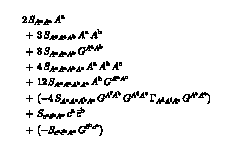

```mathematica
(MakeDSE[A[x]]);
%//Truncate//FSimplify
%//FPrint
```

# Testing

```mathematica
Get["FunKit`"]
```

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

{<|result→FEq[FTerm[S[{c,cb,A},{{p1,{c1}},{p2,{c2}},{-p1-p2,{v3,c3}}}]]],externalIndices→{x→{p1,{c1}},y→{p2,{c2}},z→{-p1-p2,{v3,c3}}},loopMomenta→{}|>,<|result→FEq[FTerm[S[{c,cb,A},{{p1,{c1}},{l1-p1,{c1354}},{-l1,{v1356,c1357}}}],Propagator[{cb,c},{{-l1+p1,{c1354}},{l1-p1,{c1361}}}],GammaN[{c,cb,A},{{-l1+p1,{c1361}},{l1+p2,{c1366}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{-l1-p2,{c1366}},{l1+p2,{c1359}}}],GammaN[{c,cb,A},{{-l1-p2,{c1359}},{p2,{c2}},{l1,{v1363,c1364}}}],Propagator[{A,A},{{-l1,{v1363,c1364}},{l1,{v1356,c1357}}}]],FTerm[S[{c,cb,A},{{p1,{c1}},{l1-p1,{c1368}},{-l1,{v1370,c1371}}}],Propagator[{cb,c},{{-l1+p1,{c1368}},{l1-p1,{c1373}}}],GammaN[{c,cb,A,A},{{-l1+p1,{c1373}},{p2,{c2}},{-p1-p2,{v3,c3}},{l1,{v1375,c1376}}}],Propagator[{A,A},{{-l1,{v1375,c1376}},{l1,{v1370,c1371}}}]],FTerm[-1,S[{c,cb,A},{{p1,{c1}},{l1-p1,{c1378}},{-l1,{v1380,c1381}}}],Propagator[{cb,c},{{-l1+p1,{c1378}},{l1-p1,{c1383}}}],GammaN[{c,cb,A},{{-l1+p1,{c1383}},{p2,{c2}},{l1-p1-p2,{v1388,c1389}}}],Propagator[{A,A},{{-l1+p1+p2,{v1388,c1389}},{l1-p1-p2,{v1385,c1386}}}],GammaN[{A,A,A},{{-l1+p1+p2,{v1385,c1386}},{-p1-p2,{v3,c3}},{l1,{v1391,c1392}}}],Propagator[{A,A},{{-l1,{v1391,c1392}},{l1,{v1380,c1381}}}]]],externalIndices→{x→{p1,{c1}},y→{p2,{c2}},z→{-p1-p2,{v3,c3}}},loopMomenta→{l1}|>}

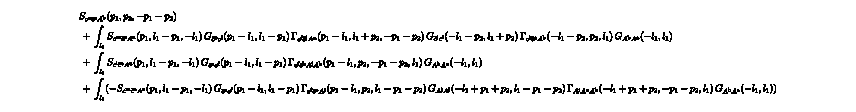

```mathematica
TakeDerivatives[MakeDSE[c[x]],{A[z],cb[y]}]//.{A[_]:>0,c[_]:>0,cb[_]:>0}//Truncate//FSimplify//Route
%//FPrint
%%//FTex;
```

```mathematica
FEq[
FTerm[FDOp[A[x]]]**FTerm[GammaN[{A,A},{a,b}]]
]//ResolveDerivatives[Setup,#]&
```

FEq[FTerm[GammaN[{A,A,A},{-x,a,b}]]]

```mathematica
fields= <|
"cField"-> {
A[p,{v, c}]
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c},{A,A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
},
S->{
{A,A},{A,A,A},{A,A,A,A},
{cb,c},{cb,c,A}
}
|>;
SetTexStyles[cb->"\\bar{c}"];
masterEquation={
{1/2 A[x]VBasis[{A,A},{-x,-y}]A[y]},
{-cb[x]VBasis[{cb,c},{-x,-y}],c[y]}
};
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation
|>;
SetGlobalSetup[Setup];
DerivativeListAcbc={ A[i1],cb[i2],c[i3]};
TakeDerivatives[Setup,WetterichEquation,DerivativeListAcbc];
%//Truncate//FSimplify//Route
%//FPrint
```

<|result→FEq[FTerm[2,Propagator[{cb,c},{{-l1-p1-p2,{c2186}},{l1+p1+p2,{c2190}}}],GammaN[{c,cb,A},{{-l1-p1-p2,{c2190}},{l1+p2,{c2197}},{p1,{v1,c1}}}],Propagator[{cb,c},{{-l1-p2,{c2197}},{l1+p2,{c2195}}}],GammaN[{c,cb,A},{{-l1-p2,{c2195}},{p2,{c2}},{l1,{v2201,c2202}}}],Propagator[{A,A},{{-l1,{v2201,c2202}},{l1,{v2192,c2193}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{l1+p1+p2,{c2199}},{-l1,{v2192,c2193}}}],Propagator[{cb,c},{{-l1-p1-p2,{c2199}},{l1+p1+p2,{c2188}}}],Rdot[{c,cb},{{-l1-p1-p2,{c2188}},{l1+p1+p2,{c2186}}}]],FTerm[-2,Propagator[{A,A},{{-l1-p1,{v2204,c2205}},{l1+p1,{v2210,c2211}}}],GammaN[{A,A,A},{{-l1-p1,{v2210,c2211}},{p1,{v1,c1}},{l1,{v2218,c2219}}}],Propagator[{A,A},{{-l1,{v2218,c2219}},{l1,{v2215,c2216}}}],GammaN[{c,cb,A},{{l1-p2,{c2224}},{p2,{c2}},{-l1,{v2215,c2216}}}],Propagator[{cb,c},{{l1-p2,{c2213}},{-l1+p2,{c2224}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{-l1+p2,{c2213}},{l1+p1,{v2221,c2222}}}],Propagator[{A,A},{{-l1-p1,{v2221,c2222}},{l1+p1,{v2207,c2208}}}],Rdot[{A,A},{{l1+p1,{v2204,c2205}},{-l1-p1,{v2207,c2208}}}]],FTerm[2,Propagator[{cb,c},{{-l1-p1-p2,{c2226}},{l1+p1+p2,{c2233}}}],GammaN[{c,cb,A,A},{{-l1-p1-p2,{c2233}},{p2,{c2}},{p1,{v1,c1}},{l1,{v2237,c2238}}}],Propagator[{A,A},{{-l1,{v2237,c2238}},{l1,{v2230,c2231}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{l1+p1+p2,{c2235}},{-l1,{v2230,c2231}}}],Propagator[{cb,c},{{-l1-p1-p2,{c2235}},{l1+p1+p2,{c2228}}}],Rdot[{c,cb},{{-l1-p1-p2,{c2228}},{l1+p1+p2,{c2226}}}]],FTerm[2,Propagator[{A,A},{{-l1,{v2240,c2241}},{l1,{v2248,c2249}}}],GammaN[{c,cb,A,A},{{l1-p1-p2,{c2254}},{p2,{c2}},{p1,{v1,c1}},{-l1,{v2248,c2249}}}],Propagator[{cb,c},{{l1-p1-p2,{c2246}},{-l1+p1+p2,{c2254}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{-l1+p1+p2,{c2246}},{l1,{v2251,c2252}}}],Propagator[{A,A},{{-l1,{v2251,c2252}},{l1,{v2243,c2244}}}],Rdot[{A,A},{{l1,{v2240,c2241}},{-l1,{v2243,c2244}}}]],FTerm[-1,Propagator[{cb,c},{{-l1-p1-p2,{c2256}},{l1+p1+p2,{c2266}}}],GammaN[{c,cb,A},{{-l1-p1-p2,{c2266}},{p2,{c2}},{l1+p1,{v2273,c2274}}}],Propagator[{A,A},{{-l1-p1,{v2273,c2274}},{l1+p1,{v2260,c2261}}}],GammaN[{A,A,A},{{-l1-p1,{v2260,c2261}},{p1,{v1,c1}},{l1,{v2268,c2269}}}],Propagator[{A,A},{{-l1,{v2268,c2269}},{l1,{v2263,c2264}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{l1+p1+p2,{c2271}},{-l1,{v2263,c2264}}}],Propagator[{cb,c},{{-l1-p1-p2,{c2271}},{l1+p1+p2,{c2258}}}],Rdot[{c,cb},{{-l1-p1-p2,{c2258}},{l1+p1+p2,{c2256}}}]],FTerm[Propagator[{A,A},{{-l1,{v2276,c2277}},{l1,{v2286,c2287}}}],GammaN[{c,cb,A},{{l1-p2,{c2294}},{p2,{c2}},{-l1,{v2286,c2287}}}],Propagator[{cb,c},{{l1-p2,{c2282}},{-l1+p2,{c2294}}}],GammaN[{c,cb,A},{{l1-p1-p2,{c2289}},{-l1+p2,{c2282}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1-p1-p2,{c2284}},{-l1+p1+p2,{c2289}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{-l1+p1+p2,{c2284}},{l1,{v2291,c2292}}}],Propagator[{A,A},{{-l1,{v2291,c2292}},{l1,{v2279,c2280}}}],Rdot[{A,A},{{l1,{v2276,c2277}},{-l1,{v2279,c2280}}}]],FTerm[-1,Propagator[{A,A},{{-l1,{v2296,c2297}},{l1,{v2305,c2306}}}],GammaN[{A,A,A},{{-l1,{v2305,c2306}},{p1,{v1,c1}},{l1-p1,{v2311,c2312}}}],Propagator[{A,A},{{-l1+p1,{v2311,c2312}},{l1-p1,{v2302,c2303}}}],GammaN[{c,cb,A,A},{{-p1-p2,{c3}},{p2,{c2}},{-l1+p1,{v2302,c2303}},{l1,{v2308,c2309}}}],Propagator[{A,A},{{-l1,{v2308,c2309}},{l1,{v2299,c2300}}}],Rdot[{A,A},{{l1,{v2296,c2297}},{-l1,{v2299,c2300}}}]]],externalIndices→{i1→{p1,{v1,c1}},i2→{p2,{c2}},i3→{-p1-p2,{c3}}},loopMomenta→{l1}|>

MaTeX::texerr: Error while running LaTeX.
! Undefined control sequence.
<argument> \unicode 
                    {f113}\text {result}\to \text {prettySuperIndices}\left ...
...opMomenta}\to \{\text{l1}\}\unicode{f114}}
!  ==> Fatal error occurred, no output PDF file produced!

$Failed